# Glauber Model

parameter set to Gold(Au)[197]
the impact parameter is set parallel to the x-axis on the reaction plane
The density ρ, thickness Ta and overlap Taa function is defined in two ways
Some optical and Monte-Carlo examples are shown

#### Define basic parameters and functions

```mathematica
A=197;
ρ0=0.169346;
R=6.38;
d=0.535;
Rmax=12;
pre=2;(*overall integration precision*)
Off[NIntegrate::inumr](*turn off some warnings*)
(*density function*)
ρ[r_]:=ρ0/(1+Exp[(r-R)/d]);
ρ[x_,y_,z_]:=
Module[{r=√(x^2+y^2+z^2)},
ρ[r]
];
(*thickness function*)
Ta[s_]:=
NIntegrate[ρ[√(s^2+z^2)],
{z,-Rmax,+Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
];
Ta[x_,y_]:=
NIntegrate[ρ[x,y,z],
{z,-Rmax,+Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
];
(*overlap function*)
Taa[b_]:=
NIntegrate[
Ta[√((x-b/2)^2+y^2)]Ta[√((x+b/2)^2+y^2)],
{x,-2Rmax,+2Rmax},{y,-2Rmax,+2Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
];
Taa[x_,y_,b_]:=Ta[√((x-b/2)^2+y^2)]Ta[√((x+b/2)^2+y^2)];
```

### Optical Glauber methods

#### density profile plots

Plots the density function profile

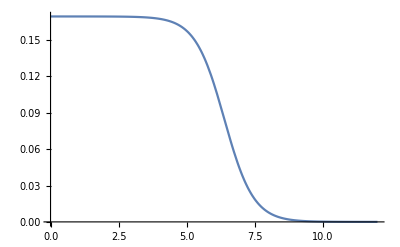

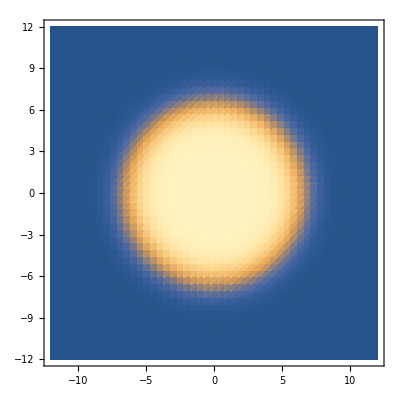

-Graphics3D-

```mathematica
Plot[ρ[r],{r,0,Rmax}]
DensityPlot[
ρ[x,y,0],
{x,-Rmax,+Rmax},{y,-Rmax,+Rmax},
PlotPoints->50
]
DensityPlot3D[
ρ[x,y,z],
{x,0,+Rmax},{y,0,+Rmax},{z,0,+Rmax},
PlotLegends->Automatic,
PlotTheme->"Scientific",
Axes->False,
ViewPoint->{-5,- 5, -5}
]
```

#### density function check

The integral of the density function should give back atomic mass

```mathematica
NIntegrate[
4π r^2 ρ[r],
{r,0,Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
NIntegrate[
ρ[x,y,z],
{x,-Rmax,+Rmax},{y,-Rmax,+Rmax},{z,-Rmax,+Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
```

{0.,196.995}

{0.015625,197.614}

#### thickness profile plot

Plots the thickness function profile

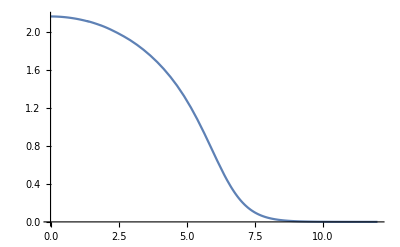

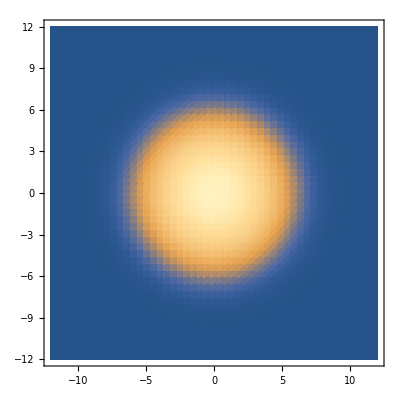

```mathematica
Plot[Ta[s],{s,0,Rmax}]
DensityPlot[Ta[x,y],{x,-Rmax,+Rmax},{y,-Rmax,+Rmax},PlotPoints->50]
```

#### thickness function check

The integral of the thickness function should also give back atomic mass

```mathematica
NIntegrate[
2π s Ta[s],
{s,0,+Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
NIntegrate[
Ta[x,y],
{x,-Rmax,+Rmax},{y,-Rmax,+Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
```

{0.015625,197.016}

{0.09375,197.348}

#### overlap profile plot

Plots the overlap function profile

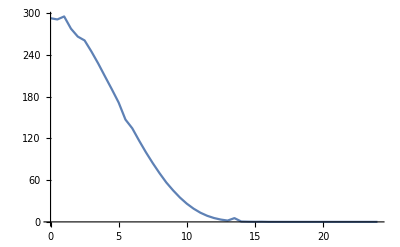

```mathematica
ListPlot[Table[{b,Taa[b]},{b,0,2Rmax,0.5}],Joined->True]
```

#### overlap function check

The integral of the overlap function should give atomic mass squared

```mathematica
NIntegrate[
2π b Taa[b],
{b,0,+2Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
NIntegrate[
2π b Taa[x,y,b],
{x,-2Rmax,+2Rmax},{y,-2Rmax,+2Rmax},{b,0,+2Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
```

{24.2344,39565.2}

{1.92188,38976.7}

#### total inelastic cross section

The total σAA with σpp set to 42mb

```mathematica
σpp=42;
NIntegrate[
2π b(1-(1-σpp Taa[b]/A^2)^(A^2)),
{b,0,2Rmax},
Method->{Automatic,"SymbolicProcessing"->0},
PrecisionGoal->pre
]//Timing
```

{12.1719,852.768}

### Monte-Carlo Glauber methods

#### Random nucleon generator

Generates A nucleons randomly by method of rejection according to density function, with given impact parameter b

```mathematica
SeedRandom[123];
RanListGen[x_,y_,z_]:=
Module[{},
ranlist={};
count=0;
While[
count<A,
rad=RandomReal[Rmax];
den=RandomReal[ρ[0]];
If[
den<=4π rad^2 ρ[rad],
θ=RandomReal[π];
ϕ=RandomReal[2π];
rx=x+rad Sin[θ]Cos[ϕ];
ry=y+rad Sin[θ]Sin[ϕ];
rz=z+rad Cos[θ];
AppendTo[ranlist,{rx,ry,rz}];
count++;
];
];
Return[ranlist];
];

impactb=10;
nucleusA=RanListGen[+impactb/2,0,-10];
nucleusB=RanListGen[-impactb/2,0,+10];
```

#### 3D visualization

Visualize the two nuclei (nucleon radius is set to 1fm)

```mathematica
Graphics3D[{Ball[nucleusA,1],Ball[nucleusB,1]}]
```

-Graphics3D-

#### 2D visualization

Visualization shown on the transverse plane, wounded and intact nucleons are differentiated

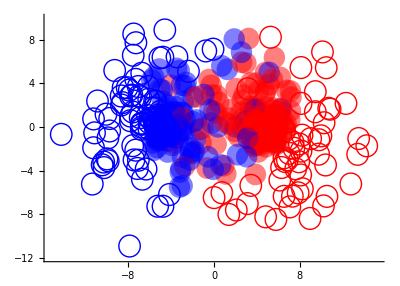

```mathematica
woundA=Table[False,A];
woundB=Table[False,A];
For[i=1,i<=A,i++,
For[j=1,j<=A,j++,
nAx=nucleusA[[i]][[1]];nAy=nucleusA[[i]][[2]];
nBx=nucleusB[[j]][[1]];nBy=nucleusB[[j]][[2]];
If[√((nAx-nBx)^2+(nAy-nBy)^2)<=2,
woundA[[i]]=True;
woundB[[j]]=True;
];
];
];
graphlist={};
For[i=1,i<=A,i++,
If[woundA[[i]],
AppendTo[graphlist,{Red,Opacity[0.5],Disk[Drop[nucleusA[[i]],-1],1]}],
AppendTo[graphlist,{Red,Circle[Drop[nucleusA[[i]],-1],1]}]
];
If[woundB[[i]],
AppendTo[graphlist,{Blue,Opacity[0.5],Disk[Drop[nucleusB[[i]],-1],1]}],
AppendTo[graphlist,{Blue,Circle[Drop[nucleusB[[i]],-1],1]}]
];
];
Graphics[graphlist,Axes->True]
```